# Introduction To Mathematica

## Part2

Notes from the Mathematica intro screencast www.wolfram.com/broadcast/screencasts/handsonstartpart2

## Formatting and Help

Use the Palettes -> Classroom Assistant -> Writing and Formatiting menu to do advanced text formatting, such as insetting new cells in other formats than input.

You can get a list of options for any cmmand using Options[Command] fx:

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/ϕ,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

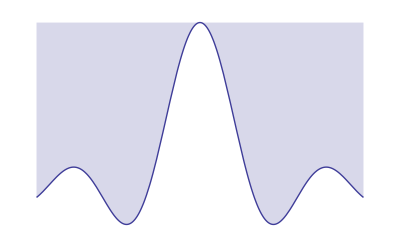

```mathematica
Plot[Sin[x]/x,{x,-10,10},Axes ->False, Filling -> Top]
```

Options can also be added via the Classroom Assistant -> Basic Commands. When plotting multiple functions on the same axis use the Tooltip function to create a tooltip that will display the function name on mouse-over

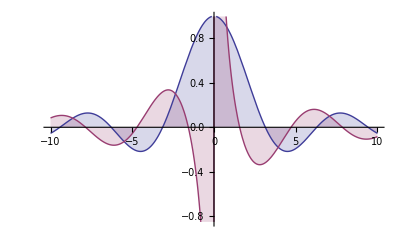

```mathematica
Plot[Tooltip[{Sin[x]/x, Cos[x]/x}], {x, -10,10},Filling->Axis]
```

## = vs == vs :=

Variable assignment "="

```mathematica
a=10/4
```

5/2

equals "=="

```mathematica
2 == 3
```

False

```mathematica
Solve[b -7 == 0,b]
```

{{b→7}}

Function assignment ":=".  (the square exponent is created via Ctrl + 6)

```mathematica
f[x_] := x^2+1
```

```mathematica
f[2]
```

5

Note that x_ means a pattern, it does not refer to any exsiting x variable

```mathematica
f[(x+1)]
```

(x+1)^2+1

## Data

We can import data from the filesystem (the path to the filesystem can be inserted via Insert -> File Path...)

```mathematica
data = Import["/Users/lt/Documents/projects/math/mathematica/data.xls"]
```

({1.,0.} | {2.,0.} | {3.,0.} | {4.,0.} | {5.,0.} | {6.,0.3} | {7.,0.4} | {8.,0.7} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,} | {,})

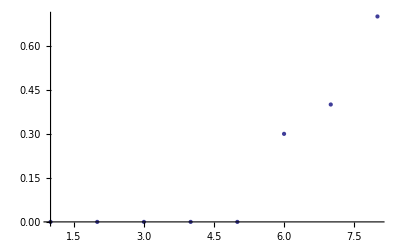

```mathematica
ListPlot[data]
```

or we can use some of Mathematica' s build in data (automcatically updated form the Internet)

```mathematica
ChemicalData[]
```

{LiquidHydrogen,MolecularHydrogen,DeuteriumHydride,LiquidHelium,Helium,Deuterium,Lithium6,Lithium,«37699»,7nMethyl8Hydroguanosine5Monophosphate,Anidulafungin,Androstanedione,BromoWillardiine,CacodylateIon,2r4AminoIminoMethylPhenylAmino5Ethoxy2Fluoro33rTetrahydrofuran3YloxyPhenylAceticacid,Ununseptium}

we can get a list of properties to apply to data via

```mathematica
ChemicalData["Properties"]
```

{AcidityConstant,AcidityConstants,AdjacencyMatrix,AlternateNames,AtomPositions,AutoignitionPoint,BeilsteinNumber,BoilingPoint,BondTally,CASNumber,CHColorStructureDiagram,CHStructureDiagram,CIDNumber,Codons,ColorStructureDiagram,CombustionHeat,CompoundFormulaDisplay,CompoundFormulaString,CriticalPressure,CriticalTemperature,Density,DensityGramsPerCC,DielectricConstant,DOTHazardClass,DOTNumbers,EdgeRules,EdgeTypes,EGECNumber,ElementMassFraction,ElementTally,ElementTypes,EUNumber,FlashPoint,FlashPointFahrenheit,FormalCharges,FormattedName,GmelinNumber,HBondAcceptorCount,HBondDonorCount,HenryLawConstant,HildebrandSolubility,HildebrandSolubilitySI,InChI,IonEquivalents,Ions,IonTally,IsoelectricPoint,IsomericSMILES,IUPACName,LogAcidityConstant,LowerExplosiveLimit,MDLNumber,MeltingBehavior,MeltingPoint,Memberships,MolarVolume,MolecularFormulaDisplay,MolecularFormulaString,MolecularWeight,MoleculePlot,Name,NFPAFireRating,NFPAHazards,NFPAHealthRating,NFPALabel,NFPAReactivityRating,NonHydrogenCount,NonStandardIsotopeCount,NonStandardIsotopeNumbers,NonStandardIsotopeTally,NSCNumber,OdorThreshold,OdorType,PartitionCoefficient,pH,Phase,RefractiveIndex,Resistivity,RotatableBondCount,RTECSClasses,RTECSNumber,SideChainAcidityConstant,SMILES,Solubility,SolubilityType,SpaceFillingMoleculePlot,StandardName,StructureDiagram,SurfaceTension,TautomerCount,ThermalConductivity,TopologicalPolarSurfaceArea,UpperExplosiveLimit,VanDerWaalsConstants,VaporDensity,VaporizationHeat,VaporPressure,VaporPressureTorr,VertexCoordinates,VertexTypes,Viscosity}

```mathematica
ChemicalData["Caffeine","MoleculePlot"]
```

```mathematica
CountryData["Denmark","Flag"]
```

-Graphics-

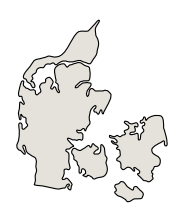

```mathematica
CountryData["Denmark","Shape"]
```

For a complete list of data go to Help -> Documentation Center -> Computable Data